(100 √(2/π) Sin[w])/w

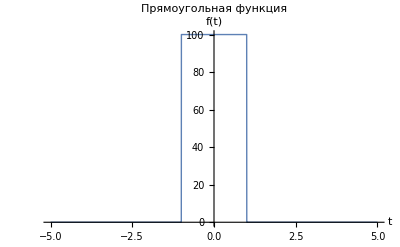

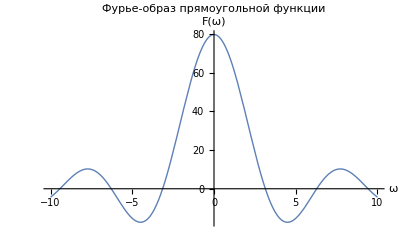

```mathematica
f[t_,a_,b_]:=Piecewise[{{a,Abs[t]≤b},{0,Abs[t]>b}}]

a=100;
b=1;

fourier=FourierTransform[f[t,a,b],t,w]

Plot[f[t,a,b],{t,-5,5},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","f(t)"},PlotLabel->"Прямоугольная функция", Exclusions->None]

Plot[Re[fourier],{w,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ω","F(ω)"},PlotLabel->"Фурье-образ прямоугольной функции"]
```

-(ⅇ^(-2 ⅈ w) (-1+ⅇ^(2 ⅈ w))^2)/(2 √(2 π) w^2)

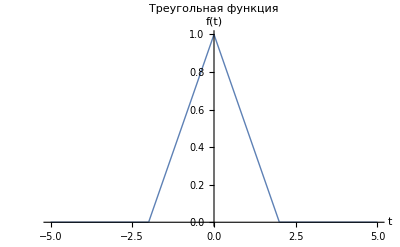

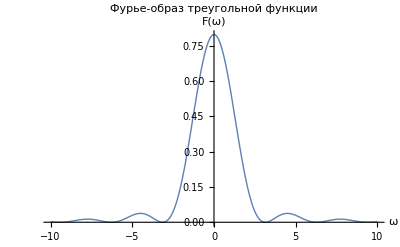

```mathematica
f[t_,a_,b_]:=Piecewise[{{a-Abs[a t/b],Abs[t]≤b},{0,Abs[t]>b}}]

a=1;
b=2;

fourier=FourierTransform[f[t,a,b],t,w]

Plot[f[t,a,b],{t,-5,5},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","f(t)"},PlotLabel->"Треугольная функция"]

Plot[Re[fourier],{w,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ω","F(ω)"},PlotLabel->"Фурье-образ треугольной функции"]
```

5/2 √(π/2) (Sign[1-w]+Sign[1+w])

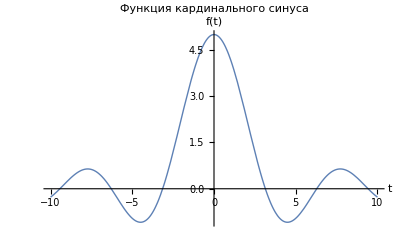

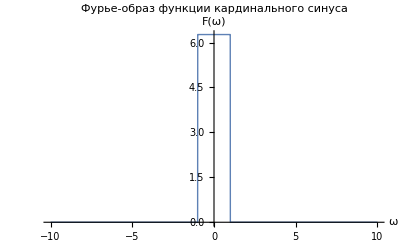

```mathematica
f[t_,a_,b_]:=a Sinc[b t]

a=5;
b=1;

fourier=FourierTransform[f[t,a,b],t,w]

Plot[f[t,a,b],{t,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","f(t)"},PlotLabel->"Функция кардинального синуса"]

Plot[Re[fourier],{w,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ω","F(ω)"},PlotLabel->"Фурье-образ функции кардинального синуса", Exclusions->None]
```

(ⅇ^(-w^2/4))/(√2)

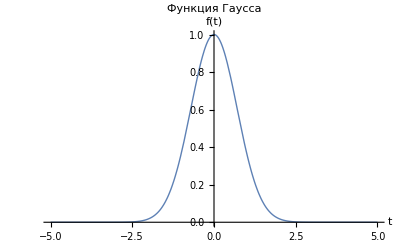

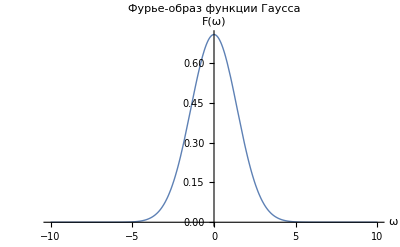

```mathematica
f[t_,a_,b_]:=a Exp[-b t^2]

a=1;
b=1;

fourier=FourierTransform[f[t,a,b],t,w]

Plot[f[t,a,b],{t,-5,5},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","f(t)"},PlotLabel->"Функция Гаусса"]

Plot[Re[fourier],{w,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ω","F(ω)"},PlotLabel->"Фурье-образ функции Гаусса"]
```

(√(2/π))/(1+w^2)

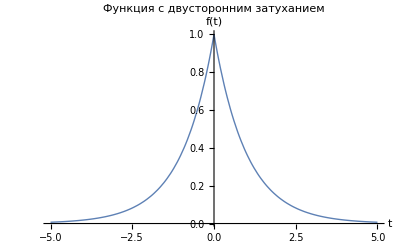

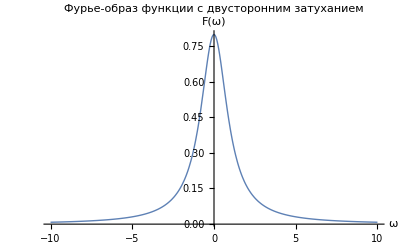

```mathematica
f[t_,a_,b_]:=a Exp[-b Abs[t]]

a=1;
b=1;

fourier=FourierTransform[f[t,a,b],t,w]

Plot[f[t,a,b],{t,-5,5},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","f(t)"},PlotLabel->"Функция с двусторонним затуханием"]

Plot[Re[fourier],{w,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ω","F(ω)"},PlotLabel->"Фурье-образ функции с двусторонним затуханием"]
```